Метод на хордите

Условия за намиране на корен на уравнението f (x) = 0  с точност ε:
1. f ∈C^2[a,b]
2. f(a).f(b) < 0
3. f'(x), f''(x) имат постоянен знак в [a,b].
Тогава итерационният процес:

x_(n+1)=x_n- (f(x_n))/(f(x_n)-f(p))(x_n-p),

n = 0,1,2,...e сходящ към единствения корен x^*на f (x)=0.
x_0 - такова, че f(x_0)f''(x)<0;
p - постоянната точка, през която минават всички хорди, тоест другият край на интервала.

За оценка на грешката имаме :
|x^*-x_n|⩽ (M_1-m_1)/m_1|x_n-x_(n-1)|=ε_n

където M_1= max_[a,b] |f'(x)|, m_1= min_[a,b] |f'(x)|.

Задача 1.
По метода на хордите да се намери с точност 0.001 положителния корен на уравнението ⅇ^x-x-1.25=0.

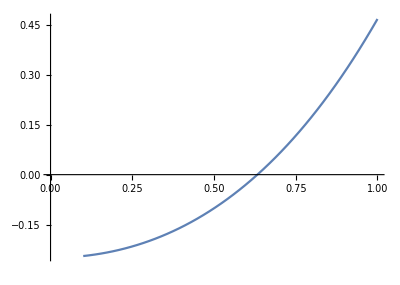

```mathematica
Clear[a,b,x0,x];
f[x_]:=ⅇ^x-x-1.25
Plot[f[x],{x,0.1,1},AxesOrigin->{0,0},AspectRatio->Automatic]
```

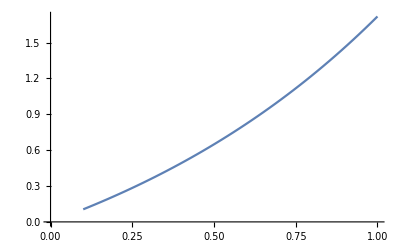

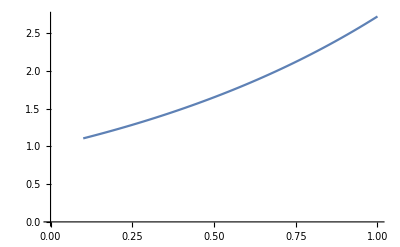

```mathematica
a=0.1;b=1.;eps=10^-4;
If[f[a]*f[b]>0,Print["Лош интервал!"]];
Plot[f'[x],{x,a,b},AxesOrigin->{0,0}]
Plot[f''[x],{x,a,b},AxesOrigin->{0,0}]
(* f'>0 за всяко x в [a,b] *)(* f''>0 за всяко x в [a,b] *)
```

```mathematica
(* Определяне на x0 *)
If[f[a]*f''[(a+b)/2]<0,x0=a,x0=b];
(* Определяме постоянната точка *)
If[x0==a,p=b,p=a];
Print[Style["Начално приближение: x0 = ",14,Blue],Style[x0,14,Blue]]
Print[Style["Неподвижен край: p = ",14,Red],Style[p,14,Red]];
err=∞;n=0;
Print["   n = ",n,"   x = ",x0,"   f[x]=",f[x0],"   err=",err];
x=x0;
While[err>eps,
n=n+1;
y=x-f[x]/(f[x]-f[p])(x-p);
err=Abs[(y-x)];x=y;
Print["   n = ",n,"   x = ",x,"   f[x]=",f[x],"   err=",err];
];
Print["Отговор x^*~ ",x, " с грешка ", err]
```

Начално приближение: x0 = 0.1

Неподвижен край: p = 1.

n = 0   x = 0.1   f[x]=-0.244829   err=∞

n = 1   x = 0.408993   f[x]=-0.153692   err=0.308993

n = 2   x = 0.555033   f[x]=-0.0630347   err=0.14604

n = 3   x = 0.607823   f[x]=-0.0213938   err=0.0527903

n = 4   x = 0.624957   f[x]=-0.00679121   err=0.0171341

n = 5   x = 0.630318   f[x]=-0.00210984   err=0.00536127

n = 6   x = 0.631977   f[x]=-0.000651076   err=0.00165813

n = 7   x = 0.632488   f[x]=-0.000200498   err=0.000510971

n = 8   x = 0.632645   f[x]=-0.0000617038   err=0.000157286

n = 9   x = 0.632693   f[x]=-0.0000189857   err=0.0000483987

Отговор x^*~ 0.632693 с грешка 0.0000483987

```mathematica
x=.
FindRoot[f[x],{x,0.5}]
```

{x→0.632715}

Задача 2 
По метода на хордите да се намери с точност 10^-4 коренът на уравнението x+ⅇ^x=0.

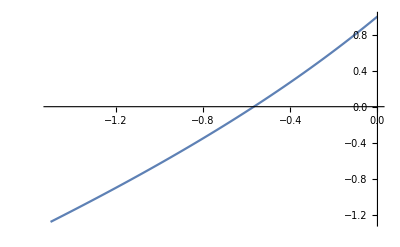

```mathematica
f[x_]:=x+ⅇ^x
Plot[f[x],{x,-1.5,0},AxesOrigin->{0,0}]
```

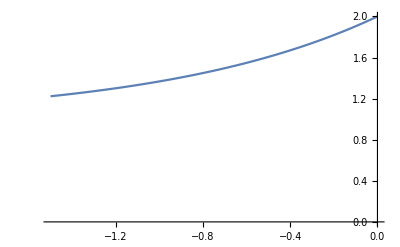

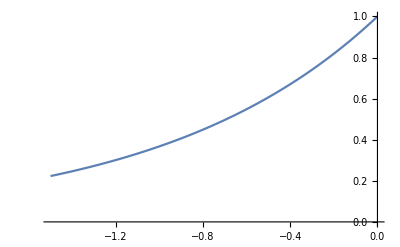

```mathematica
Clear[a,b,x0,x];
a=-1.5;b=0.;eps=10^-4;
If[f[a]*f[b]>0,Print["Лош интервал!"]];
Plot[f'[x],{x,a,b},AxesOrigin->{0,0}]
Plot[f''[x],{x,a,b},AxesOrigin->{0,0}]
```

```mathematica
(* Определяне на x0 *)
If[f[a]*f''[(a+b)/2]<0,x=a,x=b];
(* Определяме постоянната точка *)
If[x==a,p=b,p=a];
Print[Style["Начално приближение: x0 = ",14,Blue],Style[x,14,Blue]]
Print[Style["Неподвижен край: p = ",14,Blue],Style[p,14,Blue]];
err=∞;
n=0;
Print["   n = ",n,"   x = ",x,"   f[x]=",f[x],"   err=",err];
While[err>eps,
n=n+1;
y=x-f[x]/(f[x]-f[p])(x-p);
err=Abs[(y-x)];x=y;
Print["   n = ",n,"   x = ",x,"   f[x]=",f[x],"   err=",err];
];
Print["Отговор x^*~ ",x, " с грешка ", err]
```

Начално приближение: x0 = -1.5

Неподвижен край: p = 0.

n = 0   x = -1.5   f[x]=-1.27687   err=∞

n = 1   x = -0.658799   f[x]=-0.141327   err=0.841201

n = 2   x = -0.577222   f[x]=-0.0157664   err=0.081577

n = 3   x = -0.568263   f[x]=-0.001754   err=0.00895945

n = 4   x = -0.567268   f[x]=-0.000195062   err=0.000994987

n = 5   x = -0.567157   f[x]=-0.0000216921   err=0.000110631

n = 6   x = -0.567145   f[x]=-2.41227×10^-6   err=0.0000123025

Отговор x^*~ -0.567145 с грешка 0.0000123025

```mathematica
Задача 3 
По метода на хордите да се намери с точност 0.001 коренът на уравнението
 ⅇ^x-x^2-2x-2=0.
```